```mathematica
dir = SetDirectory@NotebookDirectory[];
```

```mathematica
chromosomeCoordinates = Import["/Users/lma250/Documents/Research/Backman Lab/Kyle/RD C2 12.12.21 Coordinates.xlsx"];
```

```mathematica
pixelcorrection = .119;
```

Check that the data is well organized. It should be structure so that it goes Image, Nuclei, X-coord center of nuclei, y coord center of nuclei, list of centroids of chromosomes

```mathematica
TableForm[chromosomeCoordinates[[1]]]
```

Image # | Nuclei # | Ax  | Ay  | Bx  | By  | Cx  | Cy  | Dx | Dy | Ex | Ey | Fx | Fy | Gx | Gy | Hx | Hy | Ix | Iy | Jx | Jy | Kx | Ky | Lx | Ly | Mx | My | Nx | Ny | Ox | Oy | Px | Py
3. | 1. | 884.457 | 279.566 | 880.441 | 230.209 | 915.332 | 272.534 | 906.881 | 336.659 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3. | 2. | 282.612 | 785.048 | 314.197 | 714.481 | 306.604 | 744.869 | 357.76 | 748.705 | 236.899 | 785.057 | 276.49 | 792.734 | 294.41 | 826.662 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4. | 1. | 395.484 | 390.792 | 388.473 | 326.218 | 342.57 | 350.599 | 388.3 | 365.712 | 368.628 | 392.077 | 389.081 | 406.754 | 426.577 | 427.802 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4. | 2. | 265.314 | 754.746 | 272.13 | 664.371 | 203.231 | 733.353 | 241.011 | 752.853 | 312.842 | 772.281 | 288.216 | 826.131 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4. | 3. | 672.598 | 750.111 | 652.092 | 727.322 | 691.125 | 723.981 | 693.107 | 800.055 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5. | 1. | 349.938 | 504.031 | 396.115 | 474.588 | 327.967 | 509.7 | 340.42 | 536.596 | 361.429 | 572.44 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5. | 2. | 445.675 | 729.217 | 434.701 | 711.065 | 412.476 | 764.868 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5. | 3. | 336.461 | 827.117 | 284.154 | 791.154 | 354.151 | 815.203 | 291.853 | 818.021 | 297.207 | 838.897 | 366.051 | 872.689 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6. | 1. | 857.798 | 160.411 | 850.907 | 147.778 | 881.196 | 139.179 | 872.946 | 162.643 | 807.626 | 190.769 | 797.635 | 223.244 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6. | 2. | 273.792 | 546.331 | 256.081 | 531.71 | 244.773 | 553. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6. | 3. | 282.78 | 853.173 | 260.543 | 787.794 | 269.641 | 826.993 | 198.539 | 836.06 | 318.797 | 865.488 | 370.155 | 861.85 | 238.74 | 869.172 | 285.342 | 860.658 | 342.53 | 866.894 | 297.485 | 882.008 | 364.881 | 882.783 | 274.063 | 891.923 | 331.304 | 921.715 |  |  |  |  |  | 
7. | 1. | 664.654 | 187.635 | 691.964 | 159.522 | 672.277 | 195.443 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7. | 2. | 733.329 | 342.22 | 805.701 | 317.21 | 681.597 | 342.639 | 774.821 | 369.604 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7. | 3. | 557.53 | 480.64 | 571.214 | 473.905 | 608.537 | 473.932 | 565.978 | 499.576 | 514.437 | 512.733 | 540.083 | 516.896 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7. | 4. | 561.565 | 737.914 | 580.93 | 726.405 | 619.5 | 782.424 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7. | 5. | 797.025 | 854.211 | 785.858 | 807.918 | 792.677 | 884.278 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8. | 1. | 863.514 | 306.301 | 861.447 | 282.131 | 918.702 | 299.944 | 835.478 | 342.478 | 851.048 | 351.613 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8. | 2. | 346.892 | 793.768 | 308.899 | 762.474 | 414.075 | 787.656 | 367.132 | 783.632 | 383.38 | 788.307 | 359.404 | 799.763 | 359.809 | 856.961 | 401.13 | 845.535 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10. | 1. | 113.825 | 347.214 | 130.581 | 321.524 | 84.394 | 341.287 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10. | 2. | 826.049 | 531.12 | 809.084 | 507.966 | 833.405 | 522.31 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10. | 3. | 373.172 | 664.75 | 453.028 | 636.464 | 284.685 | 659.009 | 413.769 | 679.681 | 367.386 | 698.762 | 410.583 | 722.212 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10. | 4. | 782.984 | 779.99 | 745.352 | 788.893 | 834.213 | 796.733 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
11. | 1. | 424.563 | 265.528 | 406.699 | 218.396 | 452.802 | 261.205 | 428.123 | 317.24 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
11. | 2. | 340.933 | 695.743 | 341.474 | 628.106 | 304.97 | 709.077 | 367.448 | 771.081 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
11. | 3. | 851.601 | 680.879 | 830.533 | 648.683 | 868.115 | 642.257 | 839.793 | 713.964 | 869.117 | 752.6 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
11. | 4. | 204.562 | 732.528 | 226.555 | 656.48 | 214.602 | 690.138 | 174.562 | 733.616 | 252.956 | 762.686 | 184.052 | 751.444 | 161.153 | 764.697 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12. | 1. | 586.445 | 180.836 | 562.869 | 196.098 | 609.062 | 202.694 | 542.776 | 208.603 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12. | 2. | 801.676 | 532.515 | 786.954 | 424.857 | 817. | 416.5 | 813.995 | 430.16 | 847.938 | 426.125 | 758.536 | 452.204 | 821.282 | 446.523 | 789. | 472. | 767.658 | 477.342 | 754.5 | 481.5 | 775.671 | 505.936 | 750.196 | 520.454 | 811.365 | 587.618 | 777.883 | 595.504 | 790.982 | 649.63 |  | 
12. | 3. | 127.719 | 623.601 | 55.154 | 563.565 | 131.845 | 584.973 | 77.521 | 612.645 | 120.445 | 672.973 | 164.193 | 678.537 | 197.504 | 682.121 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12. | 4. | 334.18 | 753.203 | 271.286 | 684.992 | 322.938 | 701.347 | 370.54 | 724.401 | 359.5 | 729. | 378. | 737. | 372.548 | 743.774 | 299.1 | 762.22 | 365.678 | 766.411 | 350.3 | 766.6 | 433.747 | 767.981 | 381.071 | 773.804 | 393.656 | 769.513 | 323. | 779.409 | 365.204 | 799.627 | 437.983 | 801.603
12. | 5. | 256.404 | 850.557 | 207.505 | 835.233 | 314.269 | 873.864 | 246.259 | 868.759 | 235.643 | 891.674 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13. | 1. | 262.753 | 182.801 | 303.859 | 169.032 | 210.073 | 180.183 | 313.757 | 202.45 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13. | 2. | 458.141 | 219.618 | 465.814 | 168.21 | 422.135 | 249.746 | 472.728 | 243.279 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13. | 3. | 677.638 | 351.267 | 670.535 | 300.509 | 707.407 | 375.914 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13. | 4. | 554.934 | 793.915 | 692.328 | 379.603 | 575.649 | 734.744 | 550.508 | 797.343 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Dimensions[chromosomeCoordinates2[[1]]]
```

{53,10}

```mathematica
partNuclei[pairlist_]:={pairlist[[1]],pairlist[[2]],pairlist[[3;;]]};
```

```mathematica
organizedData = Table[partNuclei[Partition[chromosomeCoordinates[[1,i]],2]],{i,2,Length[chromosomeCoordinates[[1]]]}];
```

```mathematica
organizedData[[1,1]]
```

{3.,1.}

```mathematica
distance =Table[{organizedData[[i,1]],
 pixelcorrection*EuclideanDistance[#1[[1]],#1[[2]]]&/@Select[Subsets[organizedData[[i,3]],{2}],NumericQ[#[[2,1]]]&]},{i,1,Length[organizedData]}];
angle = Table[{organizedData[[i,1]],
N[PlanarAngle[{#1[[1]],organizedData[[i,2]],#1[[2]]}]/Degree]&/@Select[Subsets[organizedData[[i,3]],{2}],NumericQ[#[[2,1]]]&]},{i,1,Length[organizedData]}];
```

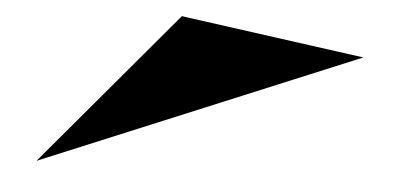

```mathematica
Graphics[Triangle[{organizedData[[3,1]],organizedData[[1,2]],organizedData[[3,2]]}]]
```

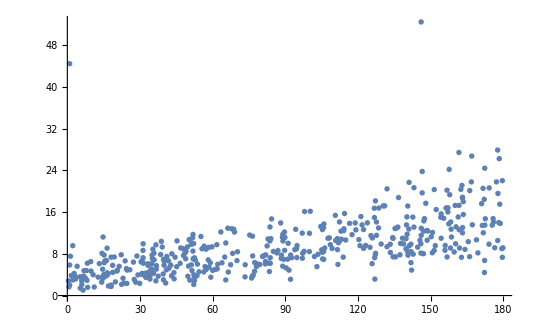

```mathematica
ListPlot[Transpose[{Flatten[Transpose[angle][[2]]],Flatten[Transpose[distance][[2]]]}], PlotRange->All]
```

```mathematica
Export[StringJoin[dir,"/distance.xlsx"],Transpose[distance]];
Export[StringJoin[dir,"/angle.xlsx"],Transpose[angle]];
```